```mathematica
Clear[x]; (* IMPORTANT! Otherwise, wrong result when evaluating total notebook *)
(* Complete Idiot's Guide To Calculus, chapter 1 *)
(* Problem 2: Find the equation of the line through point (0,–2) with slope 2/3 and put it in standard form. Answer: 2x-3y=6,
Put in x=15 and y=8 from graph below: (2*15)-(3*8)=6. 30-24=6,
Put in x=3 and y=0 from graph below: (2*3)-(3*0)=6. 6-0=6,
Put in x=0 and y=-2 from graph below: (2*0)-(3*-2)=6. 0+6=6 *)
```

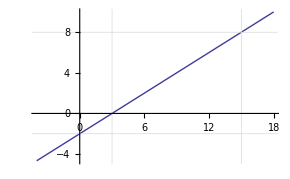

```mathematica
Plot[2/3 x-2,{x, -4, 18}, Filling -> None,
GridLines->{{3, 15},{-2, 8}},
GridLinesStyle->LightGray]
```

```mathematica
(* Problem 3 result *)
```

```mathematica
N[{-3/-4, 3/4}]
```

{0.75,0.75}

```mathematica
(* Chapter 4: Trigonometry *)
```

```mathematica
(* Degrees to radians *)
myDegrees = 57.295779513082320877;
myRadians = N[myDegrees * π/180, 10]
```

1.

```mathematica
(* Radians to degrees *)
myRadians = 1;
myDegrees = N[myRadians * 180/π, 20]
```

57.295779513082320877

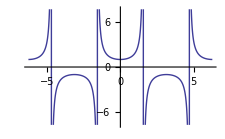

```mathematica
(* Secant graph. Secant has no x-intercepts *)
Plot[1/Cos[x], {x , -2Pi, 2Pi}]
```

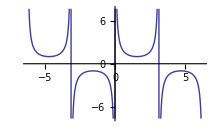

```mathematica
(* Cosecant graph. Cosecant has no x-intercepts *)
Plot[1/Sin[x], {x , -2Pi, 2Pi}]
```

```mathematica
(* Unit circle: Get the cos and sin values of the sides in a 30/60/90 triangle *)
theRadian=30 π/180; (* NOTE: Don't do N[...] here! Messes up the cosValue decimals *)
N[cosValue=Cos[theRadian], 20]
N[Sqrt[3]/2, 20]
cosValue == Sqrt[3]/2
N[sinValue=Sin[theRadian], 2]
N[1/2, 2]
```

0.86602540378443864676

0.86602540378443864676

True

0.5

0.5